```mathematica
Cos[Sin[Pi]]
Cos@Sin@Pi
Pi//Sin//Cos
Cos/@{0,Pi/2,Pi}
Cos[{0,Pi/2,Pi}]
Cos[{0,{Pi/2,Pi/2},Pi}]
```

1

1

1

{1,0,-1}

{1,0,-1}

{1,{0,0},-1}

```mathematica
FullForm[Sin/@{2,3,3}]
FullForm[Map[Sin,{2,3,3}]]
FullForm[List[Sin[2],Sin[3],Sin[3]]]
```

List[Sin[2],Sin[3],Sin[3]]

List[Sin[2],Sin[3],Sin[3]]

List[Sin[2],Sin[3],Sin[3]]

```mathematica
hf1=Plus[#,233]&
hf1/@{2,3,3}
Plus[#,233]&[233]
Grid[{#,StringLength[WikipediaData[#]]}&/@{"apple","peach","pear"}]
```

#1+233&

{235,236,236}

466

apple | 31599
peach | 22197
pear | 11606

```mathematica
hf1=#^2&
FullForm[hf1]
hf2=Function[x,x^2]
FullForm[hf2]
hf3=Function[#^2]
FullForm[hf3]
```

#1^2&

Function[Power[Slot[1],2]]

Function[x,x^2]

Function[x,Power[x,2]]

#1^2&

Function[Power[Slot[1],2]]

```mathematica
hf1=Plus[#,233]&
Array[hf1,2]
Array[hf1,{2,3}]
hf1=Plus[#1,#2]&;
Array[hf1,{2,3}]
Clear[hf1]
Clear[x]
FoldList[hf1,x,{2,3,3}]
```

#1+233&

{234,235}

{{234,234,234},{235,235,235}}

{{2,3,4},{3,4,5}}

{x,hf1[x,2],hf1[hf1[x,2],3],hf1[hf1[hf1[x,2],3],3]}

```mathematica
Clear[x,hf1]
{Head[x],MatchQ[x,x],MatchQ[x,_Symbol],MatchQ[x,_]}
{Head[233],MatchQ[233,233],MatchQ[233,_Integer],MatchQ[233,_]}
{Head[2.33],MatchQ[2.33,2.33],MatchQ[2.33,_Real],MatchQ[2.33,_]}
{Head["233"],MatchQ["233","233"],MatchQ["233",_String],MatchQ["233",_]}
{Head[hf1[x]],MatchQ[hf1[x],hf1[x]],MatchQ[hf1[x],_hf1],MatchQ[hf1[x],_]}
Head[#^2&]
```

{Symbol,True,True,True}

{Integer,True,True,True}

{Real,True,True,True}

{String,True,True,True}

{hf1,True,True,True}

Function

```mathematica
Clear[a,b,c,x,hf1]
MatchQ[{a,b},{_,b}]
MatchQ[{a,b},{_,_}]
{MatchQ[{a,a},{x_,x_}],MatchQ[{a,b},{x_,x_}]}
Cases[{{a,a},{a,b,c},{a,b}},{_,_}]
Select[{{a,a},{a,b,c},{a,b}},MatchQ[#,{_,_}]&]
MatchQ[{a,b},{a|b,a|b}]
MatchQ[{a,a,a,b},{__,b}]
MatchQ[{b},{___,b}]
MatchQ[hf1[a],_[_]]
{2,3,3}/.{2->Red,3->Green}
{a,b,b}/.{a->Red,b->Green}
```

True

True

{True,False}

{{a,a},{a,b}}

{{a,a},{a,b}}

True

True

True

«1 more identical outputs»

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}

{RGBColor[1, 0, 0],RGBColor[0, 1, 0],RGBColor[0, 1, 0]}

```mathematica
Select[#>4&][{1,2.2,3,4.5,5,6,7.5,8}]
Cases[_Integer][{2,3,2.33}]
```

{4.5,5,6,7.5,8}

{2,3}

```mathematica
Clear[f,g,x,y,z]
f[x,y,z][[2]]
Length[f[x,y,z]]
f/@g[x,y,z]
Plus@@{2,3,3}
#1->#2&@@{x,y}
f@@@{{1,2,3},{4,5,6}}
```

y

3

g[f[x],f[y],f[z]]

8

x→y

{f[1,2,3],f[4,5,6]}

<|a→6,b→2,c→3|>

<|e→5000,t→3649,a→3286,o→3153,r→2992,i→2912,n→2842,s→2599,c→1873,l→1718,m→1542,h→1496,u→1412,d→1391,p→1194,g→844,f→781,y→624,b→551,w→468,v→410,k→183,T→158,A→111,I→103,C→93,x→86,M→79,S→65,P→63,q→62,U→56,B→47,E→47,R→45,O→44,H→40,z→38,L→37,D→36,N→31,W→31,F→28,j→27,G→19,J→17,K→12,V→9,Z→8,ī→4,ū→4,Q→3,ā→2,X→1,â→1,é→1,Y→1|>

Association[Rule[a,6],Rule[b,2],Rule[c,3]]

{6,2,3}

11

<|b→2,c→3,a→6|>

<|a→6,b→2,c→3|>

{a,b,c}

{6,2,3}

{a→6,b→2,c→3}

<|a→6,b→2,c→3|>

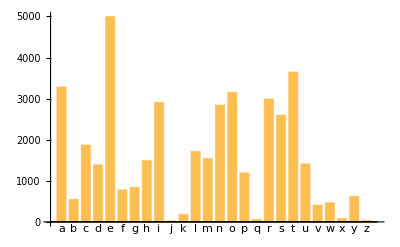

f[10,12]

```mathematica
Clear[a,b,c,z1,z2,f]
z1=Counts[{a,a,b,c,a,a,b,c,c,a,a}]
z2=LetterCounts[WikipediaData["computer"]]
FullForm[z1]
{z1[a],z1[b],z1[c]}
Total[z1]
Sort[z1]
KeySort[z1]
Keys[z1]
Values[z1]
Normal[z1]
Association[Normal[z1]]
BarChart[KeyTake[z2,Alphabet[]],ChartLabels->Automatic]
f[#apple,#orange]&[<|"apple"->10,"orange"->12,"pear"->4|>]
```

```mathematica
Clear[x]
x=1
Module[{x=Range[10]},x^2]
x
```

1

{1,4,9,16,25,36,49,64,81,100}

1

```mathematica
Clear[x,y]
x=RandomColor[];
y:=RandomColor[];
Table[x,10]
Table[y,10]
Clear[x]
{x,x,x,x}/.x->RandomReal[]
{x,x,x,x}/.x:>RandomReal[]
```

{RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767],RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767],RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767],RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767],RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767],RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767],RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767],RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767],RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767],RGBColor[0.7608309792397396, 0.0022412466273564746, 0.4706428448254767]}

{RGBColor[0.9347798218287828, 0.5439878807154928, 0.2639013332196951],RGBColor[0.6808579501564389, 0.33990098111576095, 0.7219906992748033],RGBColor[0.6924185798918359, 0.3150333605034641, 0.2309972019375255],RGBColor[0.8265988349497688, 0.002273141196066142, 0.17879112562810162],RGBColor[0.6572556003288454, 0.5542633673427078, 0.07657641393631764],RGBColor[0.766779958941262, 0.70418971118467, 0.28658104967213127],RGBColor[0.10597047182833341, 0.19032417454392125, 0.4990391259315159],RGBColor[0.4806782129688687, 0.30761871403482566, 0.23813080928608987],RGBColor[0.12002819733328107, 0.8910671469356093, 0.9917076258628794],RGBColor[0.6069711834811549, 0.30503205619572493, 0.09617000541983001]}

{0.682017,0.682017,0.682017,0.682017}

{0.962737,0.214421,0.472253,0.58478}

```mathematica
Clear[hf1]
hf1["shenmegui"]:="nidawoya"
hf1[x_RGBColor]:={x,ColorNegate[x]}
hf1[x_String]:=StringJoin["Hello world, ", x]
hf1[x_Integer]:=x+233
hf1[x_]:=x
hf1[Red]
hf1["shenmegui"]
hf1["233"]
hf1[233]
hf1[2.33]
```

{RGBColor[1, 0, 0],RGBColor[0., 1., 1.]}

nidawoya

Hello world, 233

466

2.33

```mathematica
Clear[hf1]
hf1[1]=1;
hf1[x_Integer/;x>0]:=x*hf1[x-1];
hf1[3]
hf1[1]
hf1[-1]
```

6

1

hf1[-1]

```mathematica
Clear[hf1]
hf1[x_Integer|x_Real]:=x+233
hf1[233]
hf1[2.33]
```

466

235.33

```mathematica
Clear[hf1,x,y]
hf1[1,
```

False

```mathematica
Clear[x,hf1]
hf1[x_]=x^2
hf1[10]
x=233
hf1[20]

Clear[hf1]
x=233
hf1[x_]=x^2
hf1[2(*False*)
```

x^2

100

233

400

233

54289

54289

```mathematica
Clear[hf1,hf2,hf3,x]
hf1=#^2&;
hf2[x_]=x^2;
hf3[x_]:=x^2;
FullForm[hf1]
FullForm[hf2]
FullForm[hf3]
Head[hf2]
Head[hf3]
Head[x]
```

Function[Power[Slot[1],2]]

hf2

hf3

Symbol

Symbol

Symbol

```mathematica
MatchQ[{2,3,3,3,2},{2,x__Integer,2}/;AllTrue[{x},#==3&]]
```

True

```mathematica
{3,3,3}/.x_/;AllTrue[{3,3,3},#==3&]:> Table[2,Length[x]]
{3,3,3}/.{x__Integer}/;AllTrue[{3,3,3},#==3&]:> Table[2,Length[{x}]]
```

{2,2,2}

{2,2,2}

```mathematica
Clear[hf1,x,y]
hf1[2,y:(x_)../;x==3,2]:={x,y,Length[{y}]}
hf1[2,2]
hf1[2,3,2]
hf1[2,3,3,2]
hf1[2,3,3,3,2]
```

hf1[2,2]

{3,3,1}

{3,3,3,2}

{3,3,3,3,3}

```mathematica
Clear[x,y,z,hf1]
hf1[___,x,m___,x,___]:={m}
hf1[y,y,x,y,y,x,y,y,x,y,y]

Clear[x,y,z,hf1]
hf1[___,x,Longest[m___],x,___]:={m}
hf1[y,y,x,y,y,x,y,y,x,y,y]

Clear[x,y,z,hf1]
hf1[___,x|z,m___,x|z,___]:={m}
hf1[y,y,z,y,y,x,y,y]

Clear[x,y,z,hf1]
hf1[x,y..]:=233
hf1[x,y,y,y]
```

{y,y}

{y,y,x,y,y}

{y,y}

233

```mathematica
Clear[mySort1,mySort2,x,y,z]
mySort1[xx_]:=FixedPoint[#/.{x___,b_,y___,a_,z___}/;b>a:>{x,a,y,b,z}&,xx]
mySort2=#//.{x___,a_,y___,b_,z___}:>{x,b,y,a,z}/;a>b&;
mySort1[{4,5,1,3,2}]
mySort2[{4,5,1,3,2}]
```

{1,2,3,4,5}

{1,2,3,4,5}

```mathematica
Clear[a,b,c,x]
StringCases["233+233+233","+"~~a_~~b_~~c_~~"+":>Framed[StringJoin[a,b,c]]]
StringCases["233+233+233+233","+"~~x__~~"+":>Framed[x]]
StringCases["233+233+233+233","+"~~Shortest[x__]~~"+":>Framed[x]]
StringReplace["233+233+233+233",{"+"->"<>"}]
Select[WordList[],StringMatchQ[#,"a"~~___~~"b"]&]
StringCases["233 and 0x456",DigitCharacter..]
StringCases["233 and 0x456",_~~Whitespace~~_]
StringSplit["233+233+233","+"]
StringSplit["233\n233\n233","\n"]
```

{233}

{233+233}

{233}

233<>233<>233<>233

{absorb,adsorb,adverb,alb,aplomb}

{233,0,456}

{3 a,d 0}

{233,233,233}

{233,233,233}

233
233
233

1

1

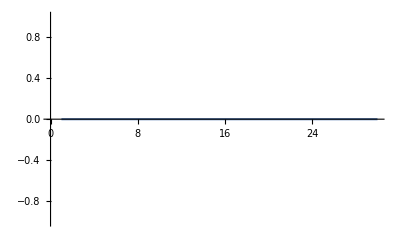

```mathematica
Clear[hf1]
hf1[1]=1
hf1[2]=1
(*hf1[n_Integer/;n>2]:=hf1[n-1]+hf1[n-2]*)
hf1[n_Integer/;n>2]:=hf1[n]=hf1[n-1]+hf1[n-2]
ListLinePlot[Table[First[Timing[hf1[n]]],{n,30}]]
```

```mathematica
StringCases[FromCharacterCode[Range[9999],"Unicode"],RegularExpression["[[:punct:]]"]]
Style[#,FontFamily->"Microsoft Uighur"]&/@%//Multicolumn[#,20]&
```

{!,",#,$,%,&,',(,),*,+,,,-,.,/,:,;,<,=,>,?,@,[,\,],^,_,`,{,|,},~,¡,§,«,¶,·,»,¿,;,·,՚,՛,՜,՝,՞,՟,։,֊,־,׀,׃,׆,׳,״,؉,؊,،,؍,؛,؞,؟,٪,٫,٬,٭,۔,܀,܁,܂,܃,܄,܅,܆,܇,܈,܉,܊,܋,܌,܍,߷,߸,߹,࠰,࠱,࠲,࠳,࠴,࠵,࠶,࠷,࠸,࠹,࠺,࠻,࠼,࠽,࠾,࡞,।,॥,॰,૰,෴,๏,๚,๛,༄,༅,༆,༇,༈,༉,༊,་,༌,།,༎,༏,༐,༑,༒,༔,༺,༻,༼,༽,྅,࿐,࿑,࿒,࿓,࿔,࿙,࿚,၊,။,၌,၍,၎,၏,჻,፠,፡,።,፣,፤,፥,፦,፧,፨,᐀,᙭,᙮,᚛,᚜,᛫,᛬,᛭,᜵,᜶,។,៕,៖,៘,៙,៚,᠀,᠁,᠂,᠃,᠄,᠅,᠆,᠇,᠈,᠉,᠊,᥄,᥅,᨞,᨟,᪠,᪡,᪢,᪣,᪤,᪥,᪦,᪨,᪩,᪪,᪫,᪬,᪭,᭚,᭛,᭜,᭝,᭞,᭟,᭠,᯼,᯽,᯾,᯿,᰻,᰼,᰽,᰾,᰿,᱾,᱿,᳀,᳁,᳂,᳃,᳄,᳅,᳆,᳇,᳓,-,‑,‒,–,—,―,‖,‗,‘,’,‚,‛,“,”,„,‟,†,‡,•,‣,․,‥,…,‧,‰,‱,′,″,‴,‵,‶,‷,‸,‹,›,※,‼,‽,‾,‿,⁀,⁁,⁂,⁃,⁅,⁆,⁇,⁈,⁉,⁊,⁋,⁌,⁍,⁎,⁏,⁐,⁑,⁓,⁔,⁕,⁖,⁗,⁘,⁙,⁚,⁛,⁜,⁝,⁞,⁽,⁾,₍,₎,⌈,⌉,⌊,⌋,⟨,⟩}

! | ; | ¡ | ֊ | ٬ | ܍ | ࠼ | ༈ | ྅ | ፡ | ᜵ | ᠈ | ᪪ | ᰼ | ‑ | ‡ | ‹ | ⁊ | ⁛ | 
" | < | § | ־ | ٭ | ߷ | ࠽ | ༉ | ࿐ | ። | ᜶ | ᠉ | ᪫ | ᰽ | ‒ | • | › | ⁋ | ⁜ | 
# | = | « | ׀ | ۔ | ߸ | ࠾ | ༊ | ࿑ | ፣ | ។ | ᠊ | ᪬ | ᰾ | – | ‣ | ※ | ⁌ | ⁝ | 
$ | > | ¶ | ׃ | ܀ | ߹ | ࡞ | ་ | ࿒ | ፤ | ៕ | ᥄ | ᪭ | ᰿ | — | ․ | ‼ | ⁍ | ⁞ | 
% | ? | · | ׆ | ܁ | ࠰ | । | ༌ | ࿓ | ፥ | ៖ | ᥅ | ᭚ | ᱾ | ― | ‥ | ‽ | ⁎ | ⁽ | 
& | @ | » | ׳ | ܂ | ࠱ | ॥ | ། | ࿔ | ፦ | ៘ | ᨞ | ᭛ | ᱿ | ‖ | … | ‾ | ⁏ | ⁾ | 
' | [ | ¿ | ״ | ܃ | ࠲ | ॰ | ༎ | ࿙ | ፧ | ៙ | ᨟ | ᭜ | ᳀ | ‗ | ‧ | ‿ | ⁐ | ₍ | 
( | \ | ; | ؉ | ܄ | ࠳ | ૰ | ༏ | ࿚ | ፨ | ៚ | ᪠ | ᭝ | ᳁ | ‘ | ‰ | ⁀ | ⁑ | ₎ | 
) | ] | · | ؊ | ܅ | ࠴ | ෴ | ༐ | ၊ | ᐀ | ᠀ | ᪡ | ᭞ | ᳂ | ’ | ‱ | ⁁ | ⁓ | ⌈ | 
* | ^ | ՚ | ، | ܆ | ࠵ | ๏ | ༑ | ။ | ᙭ | ᠁ | ᪢ | ᭟ | ᳃ | ‚ | ′ | ⁂ | ⁔ | ⌉ | 
+ | _ | ՛ | ؍ | ܇ | ࠶ | ๚ | ༒ | ၌ | ᙮ | ᠂ | ᪣ | ᭠ | ᳄ | ‛ | ″ | ⁃ | ⁕ | ⌊ | 
, | ` | ՜ | ؛ | ܈ | ࠷ | ๛ | ༔ | ၍ | ᚛ | ᠃ | ᪤ | ᯼ | ᳅ | “ | ‴ | ⁅ | ⁖ | ⌋ | 
- | { | ՝ | ؞ | ܉ | ࠸ | ༄ | ༺ | ၎ | ᚜ | ᠄ | ᪥ | ᯽ | ᳆ | ” | ‵ | ⁆ | ⁗ | ⟨ | 
. | | | ՞ | ؟ | ܊ | ࠹ | ༅ | ༻ | ၏ | ᛫ | ᠅ | ᪦ | ᯾ | ᳇ | „ | ‶ | ⁇ | ⁘ | ⟩ | 
/ | } | ՟ | ٪ | ܋ | ࠺ | ༆ | ༼ | ჻ | ᛬ | ᠆ | ᪨ | ᯿ | ᳓ | ‟ | ‷ | ⁈ | ⁙ |  | 
: | ~ | ։ | ٫ | ܌ | ࠻ | ༇ | ༽ | ፠ | ᛭ | ᠇ | ᪩ | ᰻ | - | † | ‸ | ⁉ | ⁚ |  |

```mathematica
Names["Global`*"]
```